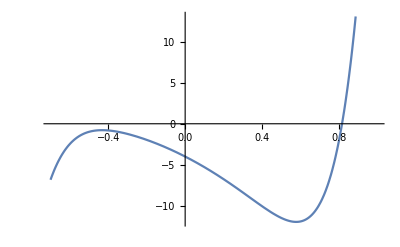

x=0.815812, итераций 6 (*для 10 в -9*)

```mathematica
f[x_]:=x^6+6 x^5+12 x^4 6 x^3-9 x^2-12x-4
Plot[f[x],{x,-0.7,1}, AxesOrigin->{0,0}]
a=0;b=1;e=0.00001;x1=b;
Do[x2=x1;
	x1=(x1-f[x1]/f'[x1])//N;
		If[Abs[x2-x1]<e,
		Print ["x=",x2 //N,", итераций " , n];
		Break[]],
{n,1,100}]
```

```mathematica
(*маленькие значения поэтому разные точности но одинаковые значения*)
```

x=0.815821, итераций 5(*-5*)

x=0.815821, итераций 5(*-4*)

x=0.815821, итераций 5(*-3*)